# Comparative Analysis of Linear Approximation and True Derivative

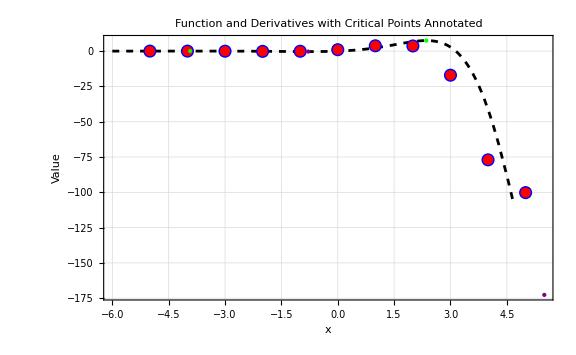

```mathematica
(*Define the function and its derivative*)
f[x_]:=Exp[x] Sin[x];
fPrime[x_]:=Exp[x] (Sin[x]+Cos[x]);

(*Data for exact and approximate derivatives at given points*)
points={-5,-4,-3,-2,-1,0,1,2,3,4,5};
exactDerivatives={0.00837248,0.00188942,-0.0563148,-0.179379,-0.110794,1,3.75605,3.64392,-17.0501,-77.0078,-100.218};
approxDerivatives={0.00837189,0.00188965,-0.0563108,-0.179376,-0.110805,1,3.75617,3.64351,-17.0488,-77.0016,-100.212};

(*Combine points with their exact and approximate derivatives*)
exactPoints=Transpose[{points,exactDerivatives}];
approxPoints=Transpose[{points,approxDerivatives}];

(*Identify local maxima and minima by finding where the derivative is zero*)
criticalPoints=x/. NSolve[fPrime[x]==0&&-6<x<6,x,Reals];

(*Evaluate the second derivative to classify maxima and minima*)
secondDeriv=D[fPrime[x],x];

(*Classify critical points*)
maximaPoints=Select[criticalPoints,(secondDeriv/. x->#)<0&];
minimaPoints=Select[criticalPoints,(secondDeriv/. x->#)>0&];

(*Prepare graphics for maxima and minima if they exist*)
maximaGraphics=If[Length[maximaPoints]>0,{Green,PointSize[Large],Point[{#,f[#]}&/@maximaPoints]},{}];
minimaGraphics=If[Length[minimaPoints]>0,{Purple,PointSize[Large],Point[{#,f[#]}&/@minimaPoints]},{}];

(*Plot the function,exact and approximate derivatives,and annotate critical points*)
funcPlot=Plot[f[x],{x,-6,6},PlotStyle->{Black,Dashed}];
exactDerivPlot=ListPlot[exactPoints,PlotStyle->{Red,PointSize[Medium]},PlotMarkers->{"●",12}];
approxDerivPlot=ListPlot[approxPoints,PlotStyle->{Blue,PointSize[Medium]},PlotMarkers->{"○",12}];

(*Show combined plot with annotations for maxima and minima*)
Show[funcPlot,exactDerivPlot,approxDerivPlot,Graphics[maximaGraphics],Graphics[minimaGraphics],PlotRange->All,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,FrameLabel->{"x","Value"},PlotLabel->"Function and Derivatives with Critical Points Annotated"]
```

From the graph, we can observe that:

The exact and approximate derivatives are very close to each other at almost all points, which indicates that the numerical approximation is quite accurate for this function within the examined range.

The critical points identified and classified as maxima (in green) and minima (in purple) help in understanding the behavior of the function. These are points where the function’s slope changes from increasing to decreasing (maxima) or from decreasing to increasing (minima).

The critical points are not only found at “flat” regions of the function (where the slope is zero) but also at points where the function’s graph has significant curvature, which is expected as these are points where the derivative (slope) changes sign.

# Comparative Analysis of Nonlinear Equation Solving Methods

Solution Accuracy:

Bisection Method: With 1 iteration, the bisection method converged to a solution of x ≈  2. This solution is quite close to the true solution computed by Mathematica.
Newton-Raphson Method: The Newton-Raphson method took 4 iterations to converge to the same solution of  x ≈ 2. Again, this result aligns closely with the Mathematica solution.
Secant Method: The secant method converged in 6 iterations to the solution x ≈ 2, which is slightly slower compared to the bisection and Newton-Raphson methods but still provides an accurate result.
2. Computational Efficiency:

Bisection Method: The bisection method took 1168 microseconds to converge, demonstrating a relatively slower computational speed due to its nature of halving the interval at each step.
Newton-Raphson Method: Newton-Raphson was the fastest among the three methods, taking only 405 microseconds to converge. However, it requires the evaluation of both the function and its derivative at each iteration.
Secant Method: The secant method took 513 microseconds to converge, which is faster than the bisection method but slightly slower than Newton-Raphson. It offers a balance between computational speed and accuracy.
3. Trade-off Between Accuracy and Speed:

Newton-Raphson vs. Secant: Although the Newton-Raphson method is faster, it requires the computation of both the function and its derivative, which might be costly for complex functions. On the other hand, the secant method approximates the derivative using finite differences, making it computationally less expensive but potentially slower in convergence. The choice between these methods depends on the trade-off between computational resources and desired accuracy.
In conclusion, while the Newton-Raphson method offers the fastest convergence, the secant method provides a balance between computational efficiency and accuracy, making it a favorable choice when function evaluations are costly. Understanding the characteristics and trade-offs of each method is crucial for selecting the most suitable approach based on specific problem requirements and constraints.

# The Bouncing Ball

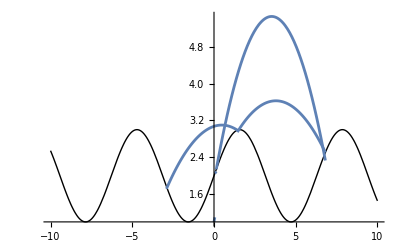

```mathematica
(*Define the gravitational constant*)g=9.81;

(*Define the parabola arc function*)
parabolaArc[x_,x0_,y0_,vx0_,vy0_]:=y0+vy0*(x-x0)/vx0-(1/2)*g*(x-x0)^2/vx0^2;

(*Define the parabolas using the given bounce data*)
parabolas={Plot[parabolaArc[x,0,1,5,10],{x,0,0.05}],Plot[parabolaArc[x,0.05,2.04998,9.00562,4.48874],{x,0.05,0.140056}],Plot[parabolaArc[x,0.140056,2.1396,4.11942,8.06491],{x,0.140056,6.81353}],Plot[parabolaArc[x,6.81353,2.50583,-6.33712,4.68787],{x,6.81353,1.42698}],Plot[parabolaArc[x,1.42698,2.98968,-6.37183,1.46668],{x,1.42698,-2.90586}]};

(*Plot the sinusoidal ground*)
ground=Plot[Sin[x]+2,{x,-10,10},PlotStyle->{Thick,Black}];

(*Combine plots*)
Show[ground,parabolas,PlotRange->All]
```

This simulation visualizes the trajectory of a ball as it bounces on a sinusoidal surface defined by the equation y=sin(x)+4, subjected to gravitational forces. The program, written in C++, employs a physics-based model to simulate the motion and interaction of the ball with the ground, factoring in both gravitational pull and the energy loss upon each bounce. This energy loss is quantified by a reflection coefficient, α=0.9, indicating that the ball retains 90% of its energy after each bounce.

Starting from an initial position of (0, 1) with an initial velocity of (5, 10), the simulation captures the ball’s trajectory through its first five bounces, adjusting its velocity according to the local slope of the surface at the point of impact and the specified energy absorption factor. The trajectory data highlights the dynamic changes in the ball’s velocity and position, showcasing a complex pattern of movement influenced by the sinusoidal ground’s shape and the physics of elastic collisions.

The Mathematica graph, derived from the simulation’s output, illustrates the ball’s path, capturing the essence of its motion across different phases - from the initial launch to subsequent bounces, each marked by distinct changes in direction and speed. The trajectory plots reveal how the combination of the ball’s initial momentum, the gravitational force, and the unique topography of the sinusoidal surface coalesce to create a fascinating pattern of bounces, each attenuated in energy but rich in dynamical complexity.